## Rain Frame Light Cones

Each coordinate system change sheds new light on the properties of the black hole. In Problem Set 15, you derived the rain-frame metric:

(Δτ)^2=(1-(2M)/r)(Δ t_rain)^2-2 √((2M)/r)Δ t_rain Δr-(Δr)^2-(r^2(Δϕ))^2

and you derived ((Δ r)/(Δ t_rain))_±=-√((2M)/r) ± 1. Of course all these derivations were only valid for small displacements, so now we may finally take the limit that the displacements go to zero, and we have found:

((d r)/(d t_rain))_±=-√((2M)/r) ± 1.

Going back to p. 3-22 where we were calling τ the wristwatch time of the raindrop, rather than calling it t_rain, we learned that

τ_2-τ_1=-∫_r_1^r_2 (√r)/(√(2M))ⅆr=-1/(√(2M))2/3(r_2^(3/2)-r_1^(3/2))

On Figure 5 on p. B-15, Taylor and Wheeler choose a raindrop that had τ_1=0 at r_1=5/2 M. Let a new variable be x=r_2/M. Then plugging these three facts in, and recognizing that what we were calling τ_2 we are now calling t_rain, we have

t_rain-0=-1/(√(2M))2/3((M^(3/2)(r_2/M))^(3/2)-(5/2 M)^(3/2))=-M/(√2)2/3(x^(3/2)-(5/2)^(3/2))

or

t_rain/M=4/3[(5/2)^(3/2)-(x/2)^(3/2)]

A bit of  a mess, but let’s plot it

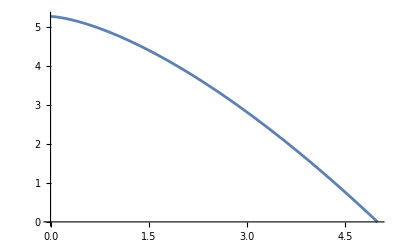

```mathematica
tRainOverM[x_,zero_]:=4/3((zero/2)^(3/2)-(x/2)^(3/2));
Plot[tRainOverM[x,5],{x,0, 5}]
```

If we want it to be a little more obvious that the function we have plotted is exactly the same as theirs, we can adjust the plot range and the aspect ratio, and label the axes:

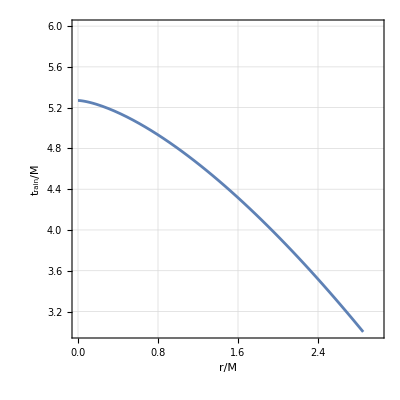

```mathematica
plot[zero_]:=
Plot[tRainOverM[x,zero],{x,0, 3}, PlotRange->{{0,3},{3,6}}, AspectRatio->1, AxesLabel->{r/M, Subscript[t, rain]/M}, GridLines->Automatic,Frame->True]
plot[5]
```

Let’s add the paths for raindrops whose wristwatches were zero when they were at 4.0M, 4.5M, 5.5M, and 6M, respectively:

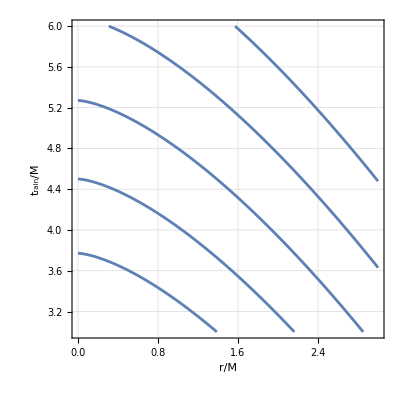

```mathematica
Show[plot[4.0],plot[4.5],plot[5.0],plot[5.5],plot[6]]
```

I apologize that the axes aren’t labeled. There is some conflict between the labels and the frame. Sigh. The horizontal axis is r/M. The vertical axis is t_rain/M.

Ink in the following five points on the middle of the five lines:

```mathematica
middle[x_]:=Round[tRainOverM[x,5],0.01];
TableForm[{
{0.5, middle[0.5]},
{1.0, middle[1.0]},
{1.5, middle[1.5]},
{2.0, middle[2.0]},
{2.5, middle[2.5]}
}]
```

0.5 | 5.1
1. | 4.8
1.5 | 4.4
2. | 3.94
2.5 | 3.41

We computed the slopes, (dr/(d t_rain))_±. Because the horizontal axis has r and the vertical axis has t, we really want the inverse of these slopes. In terms of x=r/M, the inverse slopes are:

```mathematica
slopePlus[x_]:=Round[1/(-1/(√(x/2))+1),0.01];
slopeMinus[x_]:=Round[1/(-1/(√(x/2))-1),0.01];
TableForm[{
{0.5, slopePlus[0.5], slopeMinus[0.5]},
{1.0, slopePlus[1.0], slopeMinus[1.0]},
{1.5, slopePlus[1.5], slopeMinus[1.5]},
{2.0, slopePlus[2.000002], slopeMinus[2.0]},
{2.5, slopePlus[2.5], slopeMinus[2.5]}
}]
```

0.5 | -1. | -0.33
1. | -2.41 | -0.41
1.5 | -6.46 | -0.46
2. | 2.×10^6 | -0.5
2.5 | 9.47 | -0.53

The slope that is 2 x10^6 is actually straight up. I just needed to avoid division by zero so I hacked the input a teeny bit.

You now have a total of 10 slopes, 2 for each point that you previously inked in. Add these slopes to the plot. Then draw in five pretty little light cones like Taylor and Wheeler did in Figure 5 on p. B-15. Yours won’t be in quite the same spots as theirs.